# Final Review - Multiple Linear Regression

## Credit to Zhenghao Gu (TA of VE401 SP20)

## Multiple Linear Regression

Example: We want to do physical experiment to measure the gravitational acceleration g≈9.8 m/s^2. We have several weights of 10g each. We use springs to measure their gravitational forces:

```mathematica
X={10,20,30,40,50,60,70,80};
```

```mathematica
Residual=RandomVariate[NormalDistribution[0,0.05],Length[X]]
```

{-0.0115325,0.0157878,0.0294766,-0.0597483,0.0173925,0.0349411,0.0903353,0.122338}

```mathematica
Y=0.0098*X+Residual
```

{0.0864675,0.211788,0.323477,0.332252,0.507393,0.622941,0.776335,0.906338}

```mathematica
Data=Transpose[{X,Y}]
```

{{10,0.0864675},{20,0.211788},{30,0.323477},{40,0.332252},{50,0.507393},{60,0.622941},{70,0.776335},{80,0.906338}}

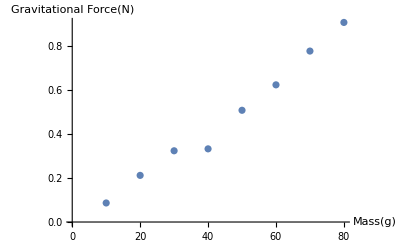

```mathematica
ListPlot[Data,AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

### Settings and Assumptions

To discuss the model

Y|x=β_0+β_1 x_1+β_2 x_2+...+β_p x_p+E

We gives the same assumptions, and define

Y=(y_1
y_2
⋮
y_n),X=(1 | x_11 | ⋯ | x_p1
1 | x_12 |   |  
⋮ | ⋮ | ⋱ | ⋮
1 | x_(1n) |   | x_pn),β=(β_0
β_1
⋮
β_p),E=(e_1
e_2
⋮
e_n)

We have Y=X β+E. Our assumptions are similar:

E[E]=0,

Var[E]=Var[Y]=σ^2 𝟙_n is constant.

E is independent of the elements of X.

### Least Squares Estimation

To minimize SS_E=(Y-X b)^T(Y-X b), we have b=(X^T X)^-1 X^T Y.

Example: I want to check whether gravitational force is related to the square of mass, so I fit my data to the model y=b_0+b_1 x+b_2 x^2. I calculate

```mathematica
y=Transpose[Data][[2]];
x=Transpose[Table[Function[x,x^k]/@Transpose[Data][[1]],{k,0,2}]];
{MatrixForm[x],MatrixForm[y]}
```

{(1 | 10 | 100
1 | 20 | 400
1 | 30 | 900
1 | 40 | 1600
1 | 50 | 2500
1 | 60 | 3600
1 | 70 | 4900
1 | 80 | 6400),(0.0864675
0.211788
0.323477
0.332252
0.507393
0.622941
0.776335
0.906338)}

```mathematica
b=Inverse[Transpose[x].x].Transpose[x].y;
MatrixForm[b]
```

(0.0350763
0.00664771
0.0000535885)

So the result become y=0.035+0.0066x+0.00005 x^2.

```mathematica
lmQuadratic=LinearModelFit[{x,y}]
```

FittedModel[0.0350763 #1+0.00664771 #2+0.0000535885 #3]

### Error Analysis

We define an orthogonal projection matrix

P=1/n(1 | 1 | ⋯ | 1
1 | 1 |   |  
⋮ | ⋮ | ⋱ | ⋮
1 | 1 |   | 1)

which can map a vector in ℝ^n to the mean of its entries. It has the nice property that P^2=P,P^T=P.

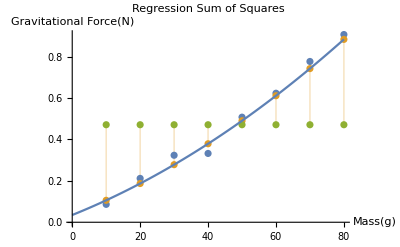

```mathematica
fit=0.035+0.0066X+0.00005 X^2;
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n];
Show[ListPlot[{Data,Transpose[{X,fit}],Transpose[{X,{repeat[Mean[Y],Length[Data]]}}]},Filling->{2->{3}}],Plot[0.035+0.0066x+0.00005 x^2,{x,0,80}],PlotLabel->"Regression Sum of Squares",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

We can then write SS_T=⟨(𝟙_n-P)Y,(𝟙_n-P)Y⟩=⟨Y,(𝟙_n-P)Y⟩. Furthermore, we define the hat matrix H=(X(X^T X))^-1 X^T, then Ŷ=X b=(X(X^T X))^-1 X^T Y=H Y.

SS_T=∑_(i=1)^n (Y_i-Ȳ)^2=⟨Y,(𝟙_n-P)Y⟩
=⟨Y,(𝟙_n-H)Y⟩+⟨Y,(H-P)Y⟩
=SS_E+SS_R
=∑_(i=1)^n (Y_i-(Ŷ)_i)^2+∑_(i=1)^n ((Ŷ)_i-Ȳ)^2

where SS_R is the regression sum of squares. Then the coefficient of multiple determination is

R^2=(SS_T-SS_E)/SS_T=SS_R/SS_T

```mathematica
lmQuadratic["RSquared"]
```

0.98973

Important Note. If you want to get R^2 directly from model[“RSquared”], use LinearModelFit instead of NonlinearModelFit.

### Distribution of Sum of Squares Error

SS_E/σ^2 follows a chi-squared distribution with n-p-1 degrees of freedom.

If β_1=β_2=⋯=β_p=0, then SS_R/σ^2 follows a chi-squared distribution with p degrees of freedom.

SS_R and SS_E are independent.

The estimator for variance S^2=SS_E/(n-p-1) is unbiased.

```mathematica
lmQuadratic["EstimatedVariance"]
```

0.00115691

### F-test for significance of Regression

Testing Parameter |  Null Hypothesis | Test Statistics
β_1,β_2,...,β_p | H_0:β_1=β_2=⋯=β_p=0 | F_(p,n-p-1)=(SS_R/p)/(SS_E/(n-p-1))=(SS_R/p)/S^2=(n-p-1)/p R^2/(1-R^2) 
 |  |

We reject H_0 if F_(p,n-p-1)>f_(α,p,n-p-1).

```mathematica
(Length[Data]-2-1)/2 lmQuadratic["RSquared"]/(1-lmQuadratic["RSquared"])
```

240.921

```mathematica
FStat=Mean[lmQuadratic["ANOVATableFStatistics"]]
```

240.921

```mathematica
1-CDF[FRatioDistribution[2,8-2-1],FStat]
```

0.000010689462543

### Distribution of Least-Squares Estimators

We have E[b]=β, meaning that it is unbiased, and

Var[b]=(σ^2(X^T X))^-1, where Var[b]=(Var[b_0] | Cov[b_0,b_1] | ⋯ | Cov[b_0,b_p]
Cov[b_0,b_1] | Var[b_1] | ⋱ | ⋮
⋮ | ⋱ | ⋱ | ⋮
Cov[b_0,b_p] | ⋯ | ⋯ | Var[b_p]) is the covariance matrix. The variance of a parameter will be Var[B_i]=ξ_ii σ^2, where ξ_ii is the (i+1)^th diagonal element of (X^T X)^-1.

The random vector b follows normal distribution.

The statistic (n-p-1)S^2/σ^2=SS_E/σ^2 is independent of b.

```mathematica
lmQuadratic["EstimatedVariance"]Inverse[Transpose[x].x]//MatrixForm
```

(0.00225183 | -0.000105361 | 1.03295×10^-6
-0.000105361 | 5.85339×10^-6 | -6.19771×10^-8
1.03295×10^-6 | -6.19771×10^-8 | 6.88634×10^-10)

```mathematica
lmQuadratic["CovarianceMatrix"]//MatrixForm
```

(0.00225183 | -0.000105361 | 1.03295×10^-6
-0.000105361 | 5.85339×10^-6 | -6.19771×10^-8
1.03295×10^-6 | -6.19771×10^-8 | 6.88634×10^-10)

### Confidence Interval of Least-Squares Estimators

The 100(1-α)% confidence intervals for the model parameters are

β_j=b_j±t_(α/2,n-p-1)S √ξ_jj,         j=0,...,p

```mathematica
lmQuadratic["ParameterConfidenceIntervalTable",ConfidenceLevel->0.95]
```

| Estimate | Standard Error | Confidence Interval
#1 | 0.0350763 | 0.0474535 | {-0.0869068,0.157059}
#2 | 0.00664771 | 0.00241938 | {0.000428496,0.0128669}
#3 | 0.0000535885 | 0.0000262418 | {-0.0000138683,0.000121045}

### Distribution of Estimated Mean

The 100(1-α)% confidence interval for the conditional mean is

(μ̂)_(Y|x_0)±t_(α/2,n-p-1) S √((x_0^T(X^T X))^-1 x_0)

With 100(1-α)% chance, the conditional mean μ_(Y|x_0) will lie in this interval.

The 100(1-α)% prediction interval for the observed value is

(μ̂)_(Y|x_0)±t_(α/2,n-p-1) S √(1+(x_0^T(X^T X))^-1 x_0)

With 100(1-α)% chance, the newly observed value Y|x_0 will lie in this interval.

```mathematica
xpredict=15;
yhat=Normal[lmQuadratic]/.{#1->1,#2->xpredict,#3->xpredict^2}
CI=lmQuadratic["MeanPredictionBands",ConfidenceLevel->0.95]/.{#1->1,#2->xpredict,#3->xpredict^2}
PI=lmQuadratic["SinglePredictionBands",ConfidenceLevel->0.95]/.{#1->1,#2->xpredict,#3->xpredict^2}
```

0.146849

{0.0899842,0.203714}

{0.04255,0.251149}

### T-Test for Model Sufficiency

Testing Parameter |  Null Hypothesis | Test Statistics
β_j | H_0:β_j=0 | T_(n-p-1)=b_j/(S √ξ_jj) 
 |  |

We reject H_0 if |T_(n-p-1)|>t_(α/2,n-p-1).

```mathematica
lmQuadratic["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 0.0350763 | 0.0474535 | 0.739173 | 0.493021
#2 | 0.00664771 | 0.00241938 | 2.74769 | 0.0404209
#3 | 0.0000535885 | 0.0000262418 | 2.0421 | 0.0966097

### Partial F-Test for Model Sufficiency

Suppose we have two models:

A full model with p+1 predictor variables

μ_(Y|x_1,...,x_p)=β_0+β_1 x_1+...+β_p x_p

A reduced model with m+1 predictor variables

μ_(Y|(x̃)_1,...,(x̃)_m)=(β̃)_0+(β̃)_1(x̃)_1+...+(β̃)_m(x̃)_m

where {(x̃)_1,...(x̃)_m}⊂{x_1,...,x_p}.

Null Hypothesis | Test Statistics
H_0:reduced model is sufficient | F_(p-m,n-p-1)=(n-p-1)/(p-m) (SS_(E,reduced)-SS_(E,full))/(SS_(E,full))=(n-p-1)/(p-m) (SS_(R,reduced)-SS_(R,full))/(SS_(R,full))  
 |

We reject H_0 if F_(p-m,n-p-1)>f_(α,p-m,n-p-1).

##### Test whether we need a quadratic model instead of a simple linear model to fit this data.

Step 1: Calculate the full and reduced model.

```mathematica
lm=LinearModelFit[Data,m,m]
```

FittedModel[-0.0453065+0.0114707 m]

```mathematica
lmQuadratic
```

FittedModel[0.0350763 #1+0.00664771 #2+0.0000535885 #3]

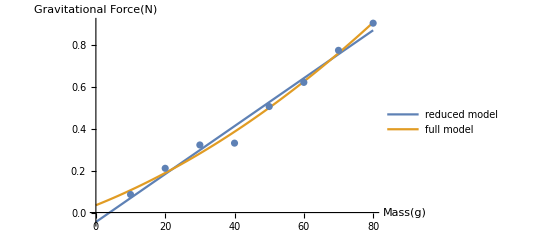

```mathematica
Show[Plot[{lm[x],lmQuadratic[1,x,x^2]},{x,0,80},PlotLegends->{"reduced model","full model"},AxesLabel->{"Mass(g)","Gravitational Force(N)"}],ListPlot[Data,AxesLabel->{"Mass(g)","Gravitational Force(N)"}]]
```

Step 2: Calculate the SS_E for both models.

```mathematica
SSEreduced=Total[lm["FitResiduals"]^2]
```

0.010609

```mathematica
SSEfull=Total[lmQuadratic["FitResiduals"]^2]
```

0.00578453

Step 3: Calculate the test statistics and critical value.

```mathematica
n=Length[Data];
p=2;m=1;
FTestStat=(n-p-1)/(p-m) (SSEreduced-SSEfull)/SSEfull
```

4.17018

```mathematica
InverseCDF[FRatioDistribution[p-m,n-p-1],0.95]
```

6.60789

Since 4.17<6.61, there is no evidence that the full model is needed.

### Indicator Variable

We can use ℓ-1 indicator variables to model ℓ levels. For example, we can define

(x_2,x_3)=Piecewise[{{(0,0), predictor is of type A,}, {(1,0), predictor is of type B,}, {(0,1), predictor is of type C,}}]

Suppose we have one numeric predictor x_1, we can set our model as

(μ̂)_(Y|x_1,x_2,x_3)=b_0+b_1 x_1+b_2 x_2+b_3 x_3

if we want the indicator to only affect intercept, or

(μ̂)_(Y|x_1,x_2,x_3)=b_0+b_1 x_1+b_2 x_2+b_3 x_3+b_4 x_1 x_2+b_5 x_1 x_3

if we want the indicator to also affect slope of x_1.

##### If we use (μ̂)_(Y|x_1,x_2,x_3)=b_0+b_1 x_1+b_2 x_2+b_3 x_3+b_4 x_1 x_2+b_5 x_1 x_3, what will be our estimation of μ_(Y|x_1,x_2,x_3)if the predictor is of type B?

Simply plug in (x_2,x_3)=(1,0) gives us (μ̂)_(Y|x_1,x_2,x_3)=b_0+b_1 x_1+b_2+b_4 x_1=(b_0+b_2)+(b_1+b_4)x_1.

### Model Selection

Goal: Choose the model that fits the data, and do well in predictions.

Methods:

Forward Selection: 
Start with the model only with β_0.
For each step, find the one variable that improves the model’s R^2 the most, and add it to the model. 
Stop the algorithm when the newly added parameter is not significant.

Backward Elimination:
Start with the full model.
For each step, find the one variable that affects the model's R^2 the most, and delete it from the model. 
Stop the algorithm when the latest deleted parameter is significant.

Stepwise Method (Not recommended).

Minimize PRESS, maximize adjusted R^2, split data into training & test sets ......

## Common Mistakes in the Assignment

### Exercise 8.2 iii)

In this case, the data {23.9,15.26}, {24.0,15.41} should NOT be considered as repeated measurements. So k should be 8, the number of distinct value of m.

# Thank you all very much for this wonderful semester. Good luck with the Final!